# Split Drive Factorials

## 0) Functions

Plots

```mathematica
PlotLineDynamics[aggregatedGroupData_,genotypeIndex_,rgbaColors_,{opacity_,thickness_},plotRange_]:=ListLinePlot[
aggregatedGroupData[[All,All,genotypeIndex]]
,AspectRatio->1/3
,Frame->True
,FrameLabel->(Style[#,50]&/@{"Time","Allele Count"})
,FrameTicksStyle->20
,FrameStyle->Thick
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Thin]
,ImageSize->1500
,InterpolationOrder->1
,PlotRange->plotRange
,PlotRangePadding->0
,PlotStyle->Directive[rgbaColors[[genotypeIndex]],Thickness[thickness],Opacity[opacity]]
]
GenerateMatrixPlotsNonNormalized[aggregatedGroupData_,timeRange_,maxesMax_]:=Module[{matrixPlots,genotypeA},
aspectRatio=7.5;
matrixPlots=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
MatrixPlot[genotypeA
,AspectRatio->1/aspectRatio
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameLabel->{
{Style["Time",.001],None},
{None,Style[Rotate["House ID",π],.001]}
}
,ImageSize->2000
,FrameTicks->{
{
Automatic,
Automatic
(*{#,#,{1,0},Directive[Thickness[.00025],Dashed]}&/@Accumulate[clustersLengths][[1;;(Length[clusters]-1)]]*)
},
{
{#,#,{1/aspectRatio,0},Directive[Thickness[.002],Dashed]}&/@{releaseTimes[[1]]},
Automatic
}
}
,FrameTicksStyle->{
{Directive[Black,40],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,40]}
}
,PlotRangePadding->None
,ColorFunction->(Blend[{rgbaColors[[i,1]],rgbaColors[[i,2]]},1.1*#1/maxPopSize]&)
,ColorFunctionScaling->False
(*,Epilog->Flatten[{Thick,Line[{{0,0},{timeRange[[2]]-1,850}}]}]*)
]
,{i,1,genotypesGroups//Length}];
matrixPlots
]
GenerateStreamChart[counts_]:=BarChart[counts//Transpose
,PerformanceGoal->"Speed"
,AspectRatio->1/4
,Axes->False
,FrameLabel->(Style[#,50]&/@{"Time","Genotype Breakdown"})
,BarSpacing->{0,0}
,ChartLayout->"Stacked"
,ChartStyle->(Directive[Opacity[.6],Lighter[#,0],EdgeForm[None]]&/@rgbColors)
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameTicks->{{None,Range[0,10000,100]},{Range[0,1.5*counts//Flatten//Max,250],None}}
,FrameTicksStyle->{
{Directive[Black,25],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,25]}
}
,GridLines->{Range[0,50000,100],Range[0,1.5*counts//Flatten//Max,100]}
,GridLinesStyle->Directive[Gray,Dashed]
,ImagePadding->Automatic
,ImageSize->2000
,PlotRangePadding->{0,0}
,PlotRange->{{timeRange[[1]],All},{0,1.1*Max[Total/@Transpose[counts]]}}
,Epilog->Flatten[{Thickness[.001],Dashed,(Line[{{#,0},{#,1.1*Max[Total/@Transpose[counts]]}}]&/@{releaseTimes[[1]]})}]
]
GenerateMatrixPlotsSplits[matrixPlots_]:=GraphicsGrid[Prepend[
Transpose[{Show[#,FrameTicks->None]&/@matrixPlots}],
{Show[matrixPlots,FrameTicks->None]}
]]
GenerateBlendSetting[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateBlendSettingCMYK[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateMatrixPlots[aggregatedGroupData_,timeRange_,maxesMax_,rgbaColors_]:=Module[{matrixPlots,genotypeA},
aspectRatio=7.5;
matrixPlots=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeA=genotypeA/maxesMax;
MatrixPlot[genotypeA
,AspectRatio->1/aspectRatio
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameLabel->{
{Style["Time",.001],None},
{None,Style[Rotate["House ID",π],.001]}
}
,ImageSize->2000
,FrameTicks->{
{
Automatic,
Automatic
(*{#,#,{1,0},Directive[Thickness[.00025],Dashed]}&/@Accumulate[clustersLengths][[1;;(Length[clusters]-1)]]*)
},
{
{#,#,{1/aspectRatio,0},Directive[Thickness[.002],Dashed]}&/@{releaseTimes[[1]]},
Automatic
}
}
,FrameTicksStyle->{
{Directive[Black,40],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,40]}
}
,PlotRangePadding->None
,ColorFunction->(Blend[{rgbaColors[[i,1]],rgbaColors[[i,2]]},1.1*#1]&)
,ColorFunctionScaling->False
(*,Epilog->Flatten[{Thick,Line[{{0,0},{timeRange[[2]]-1,850}}]}]*)
]
,{i,1,genotypesGroups//Length}];
matrixPlots
]
hexifyColor[color_RGBColor]:=StringJoin["#",IntegerString[Round[Level[color,1]*255],16,2]]
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
```

Data

```mathematica
AggregateByGenotype[rawDataTotal_,genotypesGroups_]:=Module[{aggregatedData,outputTotals,totals,transposedTotals},
outputTotals=Table[
aggregatedData=#[[All,genotypesGroups[[i,1]]]]&/@rawDataTotal;
totals=Map[Total,aggregatedData,{2}];
totals
,{i,1,genotypesGroups//Length}];
transposedTotals=Transpose/@Transpose[outputTotals];
transposedTotals
]

GetMaxPopulation[aggregatedGroupData_,genotypesGroups_,timeRange_]:=Module[{i,maxes,genotypeA,genotypeAtemp,maxesMax},
i=1;
maxes=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeAtemp=Max[#]&/@genotypeA
,{i,1,genotypesGroups//Length}];
maxesMax=Max/@Transpose[maxes];
maxesMax
]

FixDataEntry[dataFileContent_]:=Append[#,#//Total]&/@(dataFileContent[[2;;All,2;;All]][[All,1;;(Length[dataFileContent[[1]]]-1)]])
PlotDynamics[data_,ranges_,colorPalette_,plotLabels_]:=Module[{plotRight,plotLeft},
(**)
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1,
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->Large,
PlotRange->{{0,ranges[[1]]},{0,ranges[[2]]}},
FrameStyle->{
{Thick,Thick},
{Thick,Thick}
},
FrameTicks->Automatic,
FrameLabel->(Style[#,30]&/@plotLabels)
]
]
CalculateCounts[aggregatedGroupData_,genotypesGroups_]:=Module[{genotypeTemp,genotypeTotal},
Table[
genotypeTemp=aggregatedGroupData[[All,All,i]];
genotypeTotal=Total/@Transpose[genotypeTemp];
genotypeTotal
,{i,1,Length[genotypesGroups]}]
]
ImportExperimentRawData[experimentString_]:=Module[{experimentFolders,releaseTimes,rawDataExperiments,cellFolder,sweepID,filenames,rawData,rawDataTotal,genotypes,null,drive,releases,size,filenamesFemale,filenamesMale,rawDataMale,rawDataFemale,a,b,c,d,e,f},
experimentFolders=FileNames[experimentString<>"/0*",Directory[]];
releaseTimes={releasesStart,(1*releasesInterval)+releasesStart};
rawDataExperiments=Table[
cellFolder=experimentFolders[[i]];
sweepID={null,a,b,c,d,e,f}=ToExpression/@(StringSplit[StringSplit[experimentString,{"/"}],"_"]//Last);
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_*","AF1_*"};(*CHANGE TO AF1*)
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
rawDataTotal
,{i,1,experimentFolders//Length}];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&;
{rawDataExperiments,genotypes}
]
ImportExperimentRawDataByNode[experimentString_,nodePattern_]:=Module[{experimentFolders,releaseTimes,rawDataExperiments,cellFolder,sweepID,filenames,rawData,rawDataTotal,genotypes,null,drive,releases,size,filenamesFemale,filenamesMale,rawDataMale,rawDataFemale,a,b,c,d,e,f},
experimentFolders=FileNames[experimentString<>"/0*",Directory[]];
releaseTimes={releasesStart,(1*releasesInterval)+releasesStart};
rawDataExperiments=Table[
cellFolder=experimentFolders[[i]];
sweepID={null,a,b,c,d,e,f}=ToExpression/@(StringSplit[StringSplit[experimentString,{"/"}],"_"]//Last);
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Patch"<>nodePattern<>".csv","AF1_Aggregate_Patch"<>nodePattern<>".csv"};
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;TMAX,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
rawDataTotal
,{i,1,experimentFolders//Length}];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&;
{rawDataExperiments,genotypes}
]
CalculateGenotypesGroups[genotypes_]:=Module[{alleles,splits,genotypesGroups},
alleles=Flatten[StringPartition[#,1]&/@genotypes]//DeleteDuplicates;
splits=StringPartition[#,1]&/@genotypes;
genotypesGroups={
Flatten/@(Table[ConstantArray[i,Count[splits[[i]],#]]&/@alleles,{i,1,splits//Length}]//Transpose),
alleles
}//Transpose
]
CalculateGenotypesGroupsOnLocus[genotypes_,locusRange_]:=Module[{alleles,splits,genotypesGroups},
alleles=Flatten[StringPartition[#,1]&/@genotypes]//DeleteDuplicates;
splits=(StringPartition[#,1][[locusRange[[1]];;locusRange[[2]]]])&/@genotypes;
genotypesGroups={
Flatten/@(Table[ConstantArray[i,Count[splits[[i]],#]]&/@alleles,{i,1,splits//Length}]//Transpose),
alleles
}//Transpose
]
```

## 1) Load Data

```mathematica
TMAX=4000;
(*Set the path for the experiments*)
{USER,DRIVE}={3,1};
If[DRIVE==1,SetDirectory["/Volumes/marshallShare/SplitDrive/SplitDrive/2019_06_27_ANALYZED/"]]
If[DRIVE==2,SetDirectory["/Volumes/marshallShare/SplitDrive/InundativeRelease/2019_06_27_ANALYZED/"]]
If[DRIVE==3,SetDirectory["/Volumes/marshallShare/SplitDrive/CRISPR/2019_06_27_ANALYZED/"]]
(**)
If[DRIVE==1||DRIVE==2,
genotypesGroups={
{{02,05,05,06,07,12,15,15,16,17,22,25,25,26,27},"H"},
{{04,07,09,10,10,14,17,19,20,20,24,27,29,30,30},"B"},
{{03,06,08,08,09,13,16,18,18,19,23,26,28,28,29},"R"},
{{01,01,02,03,04,11,11,12,13,14,21,21,22,23,24},"W"},
{{11,12,13,14,15,16,17,18,19,20,21,21,22,22,23,23,24,24,25,25,26,26,27,27,28,28,29,29,30,30},"C"}
};
modifier=1;
{rs,releases,ri}={20,20,7};
ecoIndex=4;
]
If[DRIVE==3,
genotypesGroups={
{{02,05,05,06,07},"H"},
{{04,07,09,10,10},"B"},
{{03,06,08,08,09},"R"},
{{01,02,02,03,04},"W"}
};
modifier=1;
{rs,releases,ri}={20,1,7};
]
(*Define genotypes colors*)
originalColorsValues={
{0,100,70,0},
{50,0,50,0},
{60,100,0,0},
{10,100,0,0},
{30,20,0,0}
};
cmykColors=CMYKColor[#[[1]]/100,#[[2]]/100,#[[3]]/100,#[[4]]/100]&/@originalColorsValues;
rgbColors=ColorConvert[#,"CMYK"->"RGB"]&/@cmykColors;
Transpose[{Append[rgbColors,RGBColor[0., 0.25, 0.75]],Append[genotypesGroups[[All,2]],"Total"]}]//Grid

(**)
folderPaths=FileNames["E_*",Directory[]];
folderNames=Last[StringSplit[#,"/"]]&/@folderPaths;
folderSplits=StringSplit[#,"_"]&/@folderNames;
Length[folderSplits]
```

/Volumes/marshallShare/SplitDrive/SplitDrive/2019_06_27_ANALYZED

RGBColor[1., 0., 0.30000000000000004] | H
RGBColor[0.5, 1., 0.5] | B
RGBColor[0.4, 0., 1.] | R
RGBColor[0.9, 0., 1.] | W
RGBColor[0.7, 0.8, 1.] | C
RGBColor[0., 0.25, 0.75] | Total

78

## 2) Health Analysis

Single Run

3500

/Volumes/marshallShare/SplitDrive/SplitDrive/2019_06_27_ANALYZED/E_01_01_079_076_20_10000

{ⅇ,1,1,79,76,20,10000}

159

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30
WWWW | WWWH | WWWR | WWWB | WWHH | WWHR | WWHB | WWRR | WWRB | WWBB | WCWW | WCWH | WCWR | WCWB | WCHH | WCHR | WCHB | WCRR | WCRB | WCBB | CCWW | CCWH | CCWR | CCWB | CCHH | CCHR | CCHB | CCRR | CCRB | CCBB

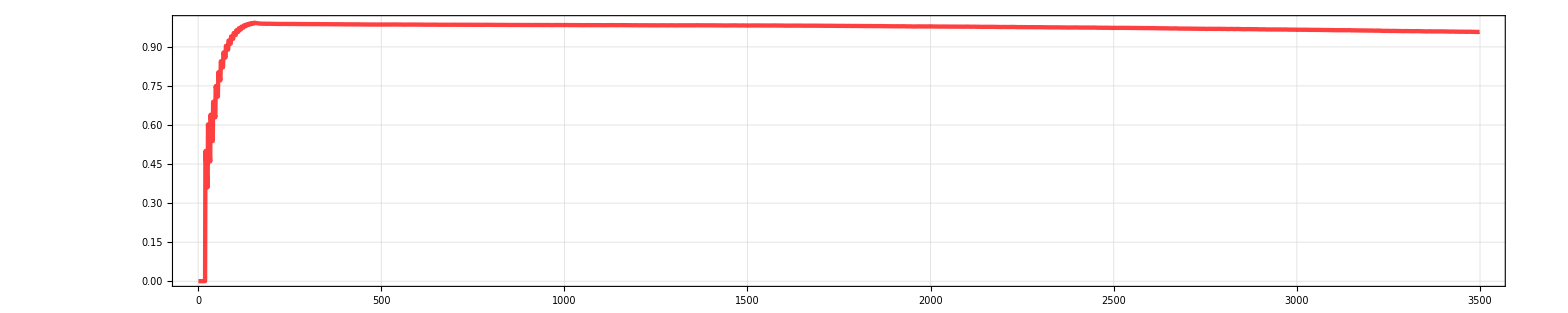

{1,79,20,3340}

```mathematica
timeLimit=3500
(**)
{patchString,threshold}={"0000",.80};
If[DRIVE==1||DRIVE==2,
genotypesGroups={
{{5,6,7,12,15,16,17,22,25,26,27},"Hx"},
{{1,2,3,4,8,9,10,11,13,14,18,19,20,21,23,24,28,29,30},"Other"}
};,
genotypesGroups={
{{2,5,6,7},"Hx"},
{{1,3,4,8,9,10},"Other"}
};
];
(*LoadExperiment*)
experimentFolders=folderPaths;
cellFolder=experimentFolders[[5]]
sweepID={null,drive,fitGRNA,femHoming,malHoming,releasesNum,mossyPerRelease}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last)
(*Releases*)
releasesEnd=rs+(releasesNum*ri)-1
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"M_Mean_Patch"<>patchString<>".csv","F_Mean_Patch"<>patchString<>".csv"};
(*LoadData*)
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;timeLimit,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&
(*AggregateData*)
aggregatedGroupData=AggregateByGenotype[rawDataTotal,genotypesGroups][[1]];
(*Suppression*)
ratios=((#[[1]])/(#[[1]]+#[[2]]))&/@aggregatedGroupData;
ListLinePlot[ratios
,AspectRatio->.2
,Frame->True
,FrameStyle->Thick
,GridLines->Automatic
,ImageSize->2000
,PlotStyle->Directive[Red,Thickness[.002],Opacity[.75]]
,PlotRange->{0,1}
]

suppressionDays=Position[(threshold<#)&/@ratios,True]//Flatten;
suppressedAfterRelease=Cases[suppressionDays,a_/;a>releasesEnd];
bounceBack=If[Length[suppressedAfterRelease]>1,suppressedAfterRelease//Last,0];
suppressionTime=bounceBack-releasesEnd;
{fitGRNA,femHoming,releasesNum,suppressionTime}
```

MultiRun

## Export Factorial

```mathematica
factorials=Table[
(**)
{patchString,threshold}={"0000",.8};
If[DRIVE==1||DRIVE==2,
genotypesGroups={
{{5,6,7,12,15,16,17,22,25,26,27},"Hx"},
{{1,2,3,4,8,9,10,11,13,14,18,19,20,21,23,24,28,29,30},"Other"}
};,
genotypesGroups={
{{2,5,6,7},"Hx"},
{{1,3,4,8,9,10},"Other"}
};
];
(*LoadExperiment*)
experimentFolders=folderPaths;
cellFolder=experimentFolders[[i]];
sweepID={null,drive,fitGRNA,femHoming,malHoming,releasesNum,mossyPerRelease}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last);
(*Releases*)
releasesEnd=rs+(releasesNum*ri)-1;
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"M_Mean_Patch"<>patchString<>".csv","F_Mean_Patch"<>patchString<>".csv"};
(*LoadData*)
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;TMAX,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&;
(*AggregateData*)
aggregatedGroupData=AggregateByGenotype[rawDataTotal,genotypesGroups][[1]];
(*Suppression*)
ratios=((#[[1]])/(#[[1]]+#[[2]]))&/@aggregatedGroupData;
suppressionDays=Position[(threshold<#)&/@ratios,True]//Flatten;
suppressedAfterRelease=Cases[suppressionDays,a_/;a>releasesEnd];
bounceBack=If[Length[suppressedAfterRelease]>1,suppressedAfterRelease//Last,0];
suppressionTime=bounceBack-releasesEnd;
{fitGRNA,femHoming,releasesNum,If[suppressionTime>0,suppressionTime,0]}
,{i,1,Length[folderPaths]}];
Export["../H_"<>ToString[DRIVE]<>"_factorials.csv",factorials]
```

../H_1_factorials.csv

## New

{{1,1,0},{1,5,2725},{1,10,3910},{1,15,3875},{1,20,3840},{1,25,3805},{2,1,0},{2,5,2237},{2,10,3444},{2,15,3875},{2,20,3840},{2,25,3805},{3,1,0},{3,5,1921},{3,10,2841},{3,15,3503},{3,20,3840},{3,25,3805},{4,1,0},{4,5,1671},{4,10,2464},{4,15,2967},{4,20,3257},{4,25,3549},{5,1,0},{5,5,1506},{5,10,2171},{5,15,2587},{5,20,2867},{5,25,3055},{6,1,0},{6,5,1243},{6,10,1745},{6,15,2059},{6,20,2269},{6,25,2397},{8,1,0},{8,5,1134},{8,10,1601},{8,15,1859},{8,20,2050},{8,25,2170},{9,1,0},{9,5,1020},{9,10,1452},{9,15,1695},{9,20,1854},{9,25,1980},{10,1,0},{10,5,869},{10,10,1248},{10,15,1439},{10,20,1590},{10,25,1658},{12,1,0},{12,5,798},{12,10,1160},{12,15,1332},{12,20,1467},{12,25,1547},{13,1,0},{13,5,726},{13,10,1083},{13,15,1240},{13,20,1370},{13,25,1437},{14,1,0},{14,5,663},{14,10,1005},{14,15,1176},{14,20,1283},{14,25,1358},{15,1,0},{15,5,611},{15,10,960},{15,15,1094},{15,20,1191},{15,25,1269}}

{{1,1,0},{1,5,2725},{1,10,3910},{1,15,3875},{1,20,3840},{1,25,3805},{2,1,0},{2,5,2237},{2,10,3444},{2,15,3875},{2,20,3840},{2,25,3805},{3,1,0},{3,5,1921},{3,10,2841},{3,15,3503},{3,20,3840},{3,25,3805},{4,1,0},{4,5,1671},{4,10,2464},{4,15,2967},{4,20,3257},{4,25,3549},{5,1,0},{5,5,1506},{5,10,2171},{5,15,2587},{5,20,2867},{5,25,3055},{6,1,0},{6,5,1243},{6,10,1745},{6,15,2059},{6,20,2269},{6,25,2397},{8,1,0},{8,5,1134},{8,10,1601},{8,15,1859},{8,20,2050},{8,25,2170},{9,1,0},{9,5,1020},{9,10,1452},{9,15,1695},{9,20,1854},{9,25,1980},{10,1,0},{10,5,869},{10,10,1248},{10,15,1439},{10,20,1590},{10,25,1658},{12,1,0},{12,5,798},{12,10,1160},{12,15,1332},{12,20,1467},{12,25,1547},{13,1,0},{13,5,726},{13,10,1083},{13,15,1240},{13,20,1370},{13,25,1437},{14,1,0},{14,5,663},{14,10,1005},{14,15,1176},{14,20,1283},{14,25,1358},{15,1,0},{15,5,611},{15,10,960},{15,15,1094},{15,20,1191},{15,25,1269},{1,0,0},{2,0,0},{3,0,0},{4,0,0},{5,0,0},{6,0,0},{8,0,0},{9,0,0},{10,0,0},{12,0,0},{13,0,0},{14,0,0},{15,0,0}}

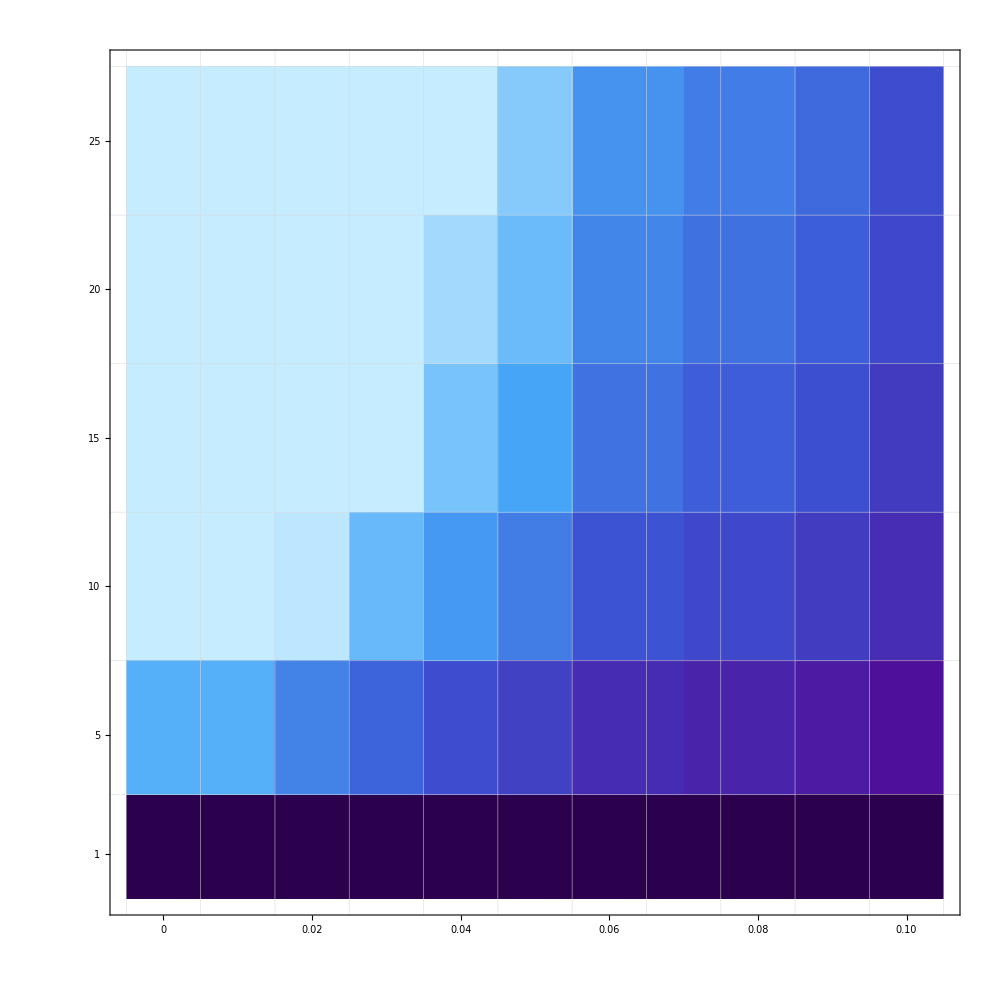

../images/H_1DensityPlot.png

```mathematica
factorials=Import["../H_"<>ToString[DRIVE]<>"_factorials.csv"];
filtered=Cases[factorials,{a_,79,b_,c_}->{a,b,c}](*//DeleteCases[#,{_,1,_}]&*)
filtered=Flatten[{filtered,{#,0,0}&/@filtered[[All,1]]//DeleteDuplicates},1]
plot=ListDensityPlot[filtered
,ColorFunction->ColorData[{"DeepSeaColors",{0,timeLimit}}]
,ColorFunctionScaling->False
(*,FrameLabel->(Style[#,20]&/@{"gRNA Fitness","Homing"})*)
,FrameStyle->Thick
,FrameTicksStyle->Directive[Gray,125]
,FrameTicks->{
{{{1,"1 "},{5,"5 "},{10,"10 "},{15,"15 "},{20,"20 "},{25,"25 "}},None},
{{{0,Rotate["0",90Degree]},{2,Rotate["0.02",90Degree]},{4,Rotate["0.04",90Degree]},{6,Rotate["0.06",90Degree]},{8,Rotate["0.08",90Degree]},{10,Rotate["0.10",90Degree]}},None}
}
,GridLines->{Range[-1.5,11,1],Flatten[{Range[2.5,30,5][[2;;All]],-2,3}]}
,GridLinesStyle->Directive[Thick,Opacity[.75],LightGray]
,ImagePadding->Automatic
,ImageSize->1000
,InterpolationOrder->0
,PlotRange->{{-.5,10.5},{-.5,27.5},{0,4000}}
,PlotRangePadding->None
,PlotRangeClipping->False
]
Export["../images/H_"<>ToString[DRIVE]<>"DensityPlot.png",plot,ImageSize->1500,ImageResolution->200]
bl=BarLegend[{"DeepSeaColors",{0,timeLimit}}];
Export["../images/bar"<>".png",bl,ImageSize->5000,ImageResolution->500]
```

```mathematica
bl=BarLegend[{"DeepSeaColors",{0,timeLimit}}];
Export["../H_bar"<>".png",bl,ImageSize->5000,ImageResolution->500];
```

## 3) Ecology Analysis

Single Run

```mathematica
timeLimit=4375
(**)
{patchString,threshold}={"0000",.8};
If[DRIVE==1||DRIVE==2,
genotypesGroups={
{{01,01,02,03,04,11,11,12,13,14,21,21,22,23,24},"W"},
{{02,05,05,06,07,12,15,15,16,17,22,25,25,26,27,04,07,09,10,10,14,17,19,20,20,24,27,29,30,30,03,06,08,08,09,13,16,18,18,19,23,26,28,28,29},"Other"}
};,
genotypesGroups={
{{01,01,02,03,04},"W"},
{{2,5,5,6,7,4,7,9,10,10,6,8,8,9,3},"Other"}
};;
];
(*LoadExperiment*)
experimentFolders=folderPaths;
cellFolder=experimentFolders[[10]]
sweepID={null,drive,fitGRNA,femHoming,malHoming,releasesNum,mossyPerRelease}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last)
(*Releases*)
releasesEnd=rs+(releasesNum*(ri+1))
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Mean_Patch"<>patchString<>".csv","AF1_Mean_Patch"<>patchString<>".csv"};
(*LoadData*)
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&
(*AggregateData*)
aggregatedGroupData=AggregateByGenotype[rawDataTotal,genotypesGroups][[1]];
(*Suppression*)
ratios=((#[[2]])/(#[[1]]+#[[2]]))&/@aggregatedGroupData;
ListLinePlot[ratios
,AspectRatio->.2
,Frame->True
,FrameStyle->Thick
,GridLines->Automatic
,ImageSize->2000
,PlotStyle->Directive[Red,Thickness[.002],Opacity[.75]]
,PlotRange->{0,1}
]

suppressionDays=Position[(threshold<#)&/@ratios,True]//Flatten;
suppressedAfterRelease=Cases[suppressionDays,a_/;a>releasesEnd];
bounceBack=If[Length[suppressedAfterRelease]>1,suppressedAfterRelease//Last,0];
suppressionTime=bounceBack-releasesEnd;
{fitGRNA,femHoming,releasesNum,suppressionTime}
```

4375

/Volumes/marshallShare/SplitDrive/SplitDrive/2019_06_27_ANALYZED/E_01_02_079_076_15_10000

{ⅇ,1,2,79,76,15,10000}

140

Part::partw: Part 1 of {} does not exist.

Import::chtype: First argument {}⟦1⟧ is not a valid file, directory, or URL specification.

Part::partd: Part specification $Failed⟦1,2;;All⟧ is longer than depth of object.

Grid[{{1,2,3},$Failed⟦1,2;;All⟧},Frame→All]

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression (1⟦2⟧)/(1⟦1⟧+1⟦2⟧) cannot be used as a part specification.

ListLinePlot::lpn: ({}⟦2⟧)/({}⟦1⟧+{}⟦2⟧)⟦(1⟦2⟧)/(1⟦1⟧+1⟦2⟧)⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

ListLinePlot[({}⟦2⟧)/({}⟦1⟧+{}⟦2⟧)⟦(1⟦2⟧)/(1⟦1⟧+1⟦2⟧)⟧,AspectRatio→0.2,Frame→True,FrameStyle→Thickness[Large],GridLines→Automatic,ImageSize→2000,PlotStyle→Directive[RGBColor[1, 0, 0],Thickness[0.002],Opacity[0.75]],PlotRange→{0,1}]

Part::pkspec1: The expression 0.8<(1⟦2⟧)/(1⟦1⟧+1⟦2⟧) cannot be used as a part specification.

{2,79,15,-140}

MultiRun

## Export Factorial

```mathematica
factorials=Table[
(**)
{patchString,threshold}={"0000",.8};
If[DRIVE==1||DRIVE==2,
genotypesGroups={
{{01,01,02,03,04,11,11,12,13,14,21,21,22,23,24},"W"},
{{02,05,05,06,07,12,15,15,16,17,22,25,25,26,27,04,07,09,10,10,14,17,19,20,20,24,27,29,30,30,03,06,08,08,09,13,16,18,18,19,23,26,28,28,29},"Other"}
};,
genotypesGroups={
{{01,01,02,03,04},"W"},
{{2,5,5,6,7,4,7,9,10,10,6,8,8,9,3},"Other"}
};;
];
(*LoadExperiment*)
experimentFolders=folderPaths;
cellFolder=experimentFolders[[i]];
sweepID={null,drive,fitGRNA,femHoming,malHoming,releasesNum,mossyPerRelease}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last);
(*Releases*)
releasesEnd=rs+(releasesNum*(ri+1));
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"M_Mean_Patch"<>patchString<>".csv","F_Mean_Patch"<>patchString<>".csv"};
(*LoadData*)
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&;
(*AggregateData*)
aggregatedGroupData=AggregateByGenotype[rawDataTotal,genotypesGroups][[1]];
(*Suppression*)
ratios=((#[[2]])/(#[[1]]+#[[2]]))&/@aggregatedGroupData;
suppressionDays=Position[(threshold<#)&/@ratios,True]//Flatten;
suppressedAfterRelease=Cases[suppressionDays,a_/;a>releasesEnd];
bounceBack=If[Length[suppressedAfterRelease]>1,suppressedAfterRelease//Last,0];
suppressionTime=bounceBack-releasesEnd;
{fitGRNA,femHoming,releasesNum,If[suppressionTime>0,suppressionTime,0]}
,{i,1,Length[folderPaths]}];
Export["../E_"<>ToString[DRIVE]<>"_factorials.csv",factorials]
```

../E__factorials.csv

## New

{{0,1,4351},{0,5,4319},{0,10,4279},{0,15,4239},{0,20,4199},{0,25,4159},{1,1,4351},{1,5,4319},{1,10,4279},{1,15,4239},{1,20,4199},{1,25,4159},{2,1,4351},{2,5,4319},{2,10,4279},{2,15,4239},{2,20,4199},{2,25,4159},{3,1,4351},{3,5,4319},{3,10,4279},{3,15,4239},{3,20,4199},{3,25,4159},{4,1,4351},{4,5,4319},{4,10,4279},{4,15,4239},{4,20,4199},{4,25,4159},{5,1,4351},{5,5,4319},{5,10,4279},{5,15,4239},{5,20,4199},{5,25,4159},{6,1,4351},{6,5,4319},{6,10,4279},{6,15,4239},{6,20,4199},{6,25,4159},{7,1,4351},{7,5,4319},{7,10,4279},{7,15,4239},{7,20,4199},{7,25,4159},{8,1,4351},{8,5,4319},{8,10,4279},{8,15,4239},{8,20,4199},{8,25,4159},{9,1,4351},{9,5,4319},{9,10,4279},{9,15,4239},{9,20,4199},{9,25,4159}}

{{0,1,4351},{0,5,4319},{0,10,4279},{0,15,4239},{0,20,4199},{0,25,4159},{1,1,4351},{1,5,4319},{1,10,4279},{1,15,4239},{1,20,4199},{1,25,4159},{2,1,4351},{2,5,4319},{2,10,4279},{2,15,4239},{2,20,4199},{2,25,4159},{3,1,4351},{3,5,4319},{3,10,4279},{3,15,4239},{3,20,4199},{3,25,4159},{4,1,4351},{4,5,4319},{4,10,4279},{4,15,4239},{4,20,4199},{4,25,4159},{5,1,4351},{5,5,4319},{5,10,4279},{5,15,4239},{5,20,4199},{5,25,4159},{6,1,4351},{6,5,4319},{6,10,4279},{6,15,4239},{6,20,4199},{6,25,4159},{7,1,4351},{7,5,4319},{7,10,4279},{7,15,4239},{7,20,4199},{7,25,4159},{8,1,4351},{8,5,4319},{8,10,4279},{8,15,4239},{8,20,4199},{8,25,4159},{9,1,4351},{9,5,4319},{9,10,4279},{9,15,4239},{9,20,4199},{9,25,4159},{0,0,0},{1,0,0},{2,0,0},{3,0,0},{4,0,0},{5,0,0},{6,0,0},{7,0,0},{8,0,0},{9,0,0}}

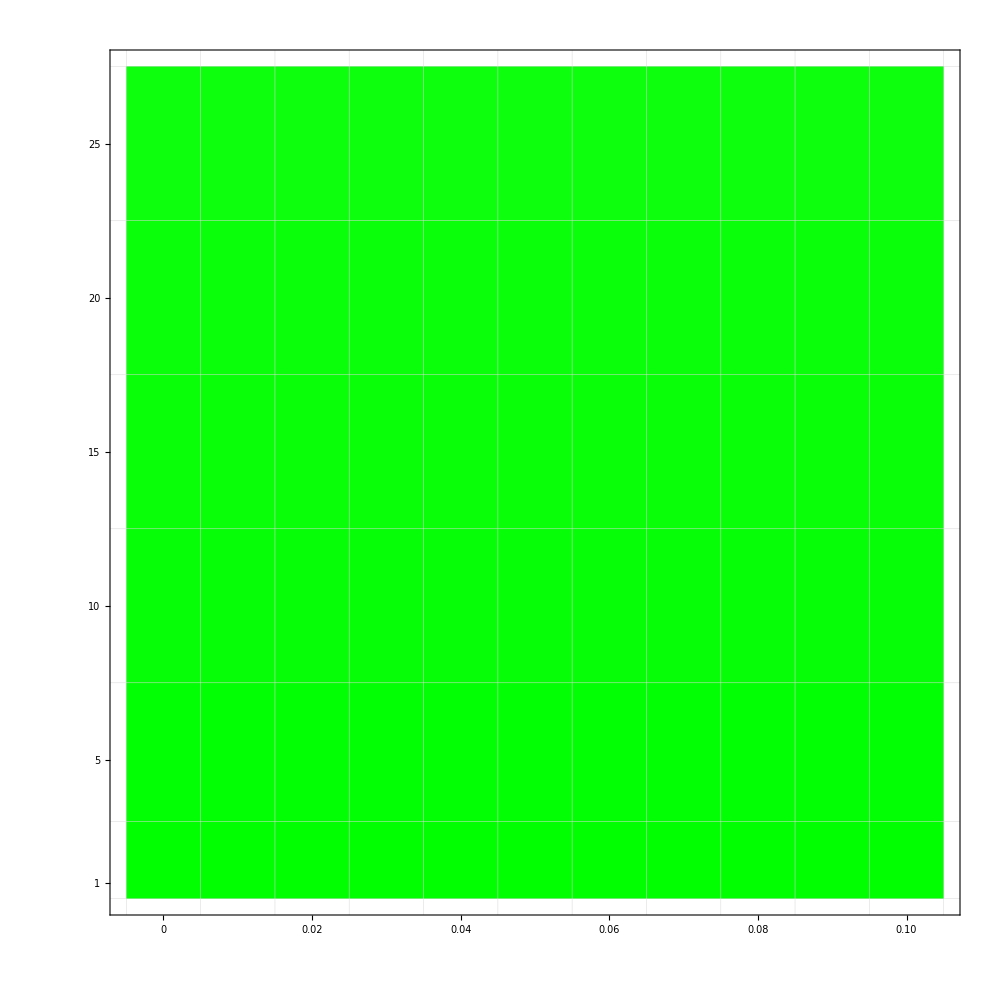

../E_DensityPlot.png

../E_bar.png

```mathematica
factorials=Import["../E__factorials.csv"];
filtered=Cases[factorials,{a_,61,b_,c_}->{a,b,c}](*//DeleteCases[#,{_,1,_}]&*)
filtered=Flatten[{filtered,{#,0,0}&/@filtered[[All,1]]//DeleteDuplicates},1]
plot=ListDensityPlot[filtered
,ColorFunction->(Blend[{{0,RGBColor[1,1,1]},{timeLimit,RGBColor[0,1,0]}},#1]&)
,ColorFunctionScaling->False
(*,FrameLabel->(Style[#,20]&/@{"gRNA Fitness","Homing"})*)
,FrameStyle->Thick
,FrameTicksStyle->Directive[Gray,125]
,FrameTicks->{
{{{1,"1 "},{5,"5 "},{10,"10 "},{15,"15 "},{20,"20 "},{25,"25 "}},None},
{{{0,Rotate["0",90Degree]},{2,Rotate["0.02",90Degree]},{4,Rotate["0.04",90Degree]},{6,Rotate["0.06",90Degree]},{8,Rotate["0.08",90Degree]},{10,Rotate["0.10",90Degree]}},None}
}
,GridLines->{Range[-1.5,11,1],Flatten[{Range[2.5,30,5][[2;;All]],.5,3}]}
,GridLinesStyle->Directive[Thick,Opacity[.75],LightGray]
,ImagePadding->Automatic
,ImageSize->1000
,InterpolationOrder->0
,PlotRange->{{-.5,10.5},{.5,27.5},{0,timeLimit}}
,PlotRangePadding->None
,PlotRangeClipping->False
]
Export["../images/E_"<>ToString[DRIVE]<>"DensityPlot.png",plot,ImageSize->1500,ImageResolution->200]
bl=BarLegend[{(Blend[{{0,RGBColor[1,1,1]},{timeLimit,RGBColor[0,1,0]}},#1]&),{0,timeLimit}},50]
Export["../images/E_bar"<>".png",bl,ImageSize->5000,ImageResolution->500]
```